{√2,0}

{1/(√2),√(3/2)}

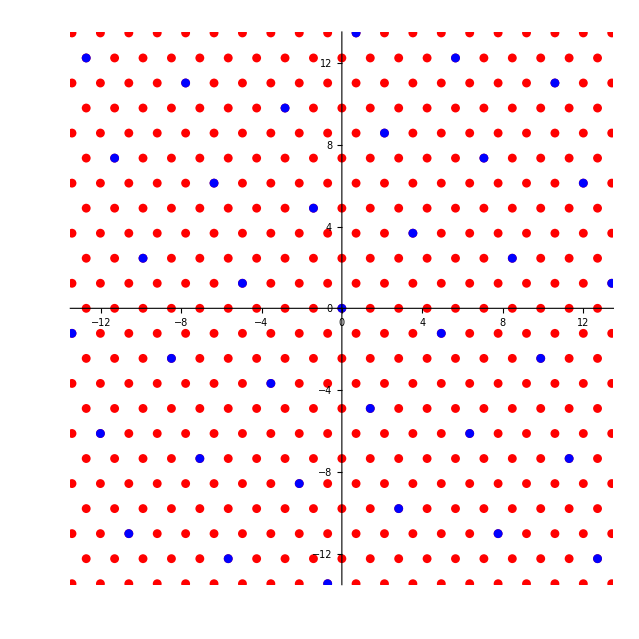

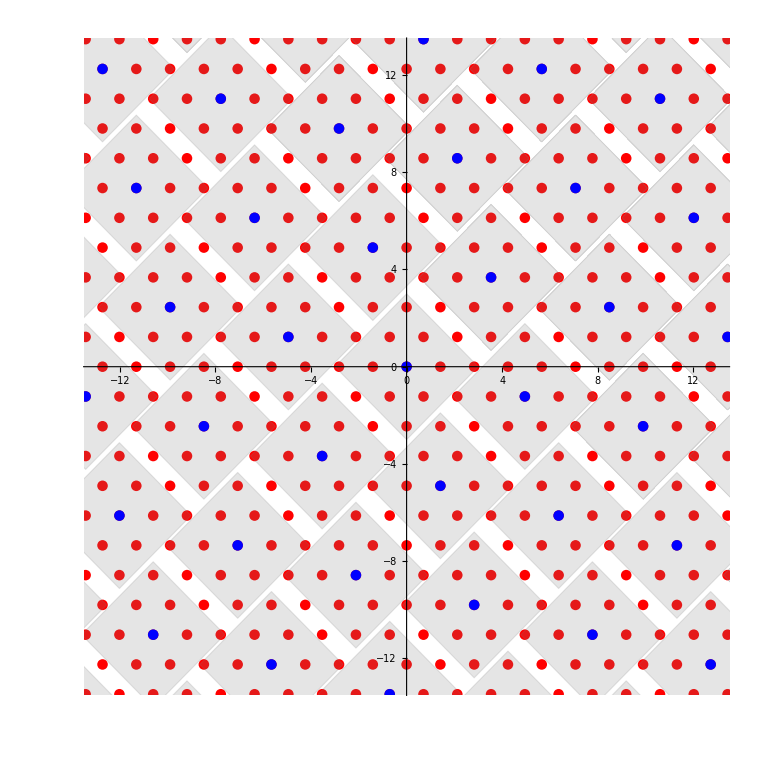

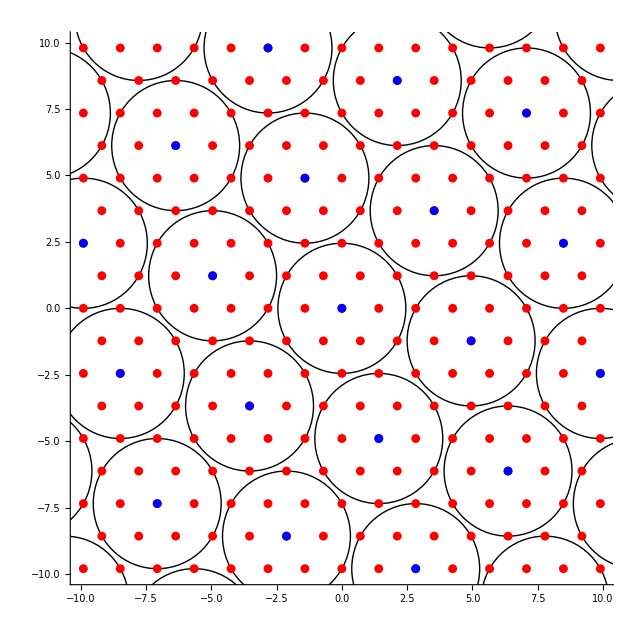

Set::wrsym: Symbol C is Protected.

```mathematica
w1={1,1};
w2={1,-1};

v1 = {Sqrt[2],0}
v2 = {Sqrt[2]/2,Sqrt[6]/2}
varMax=20;
Reticulado=Select[Flatten[Table[i*v1+j*v2,{i,-varMax,varMax},{j,-varMax,varMax}],1],Max[Abs[#]]≤25&];
DesenhoReticulado=ListPlot[Reticulado,AspectRatio->1,PlotStyle->{Red,PointSize[0.01]},GridLines->{Range[-25,25],Range[-25,25]},PlotRange->{{-13,13},{-13,13}}];


v3={-Sqrt[2],2*Sqrt[6]};
v4={-13*Sqrt[2]/2,13*Sqrt[6]/2};
varMax=25;
Reticulado2=Select[Flatten[Table[i*v3+j*v4,{i,-varMax,varMax},{j,-varMax,varMax}],1],Max[Abs[#]]≤25&];
DesenhoReticulado2=ListPlot[Reticulado2,AspectRatio->1,PlotStyle->{Blue,PointSize[0.01]},GridLines->{Range[-25,25],Range[-25,25]},PlotRange->{{-13,13},{-13,13}}];

Show[DesenhoReticulado,DesenhoReticulado2]

BolaLee[r_,c_]:=Graphics[{Thickness[0.005],Opacity[0.2],FaceForm[Gray],EdgeForm[Directive[Gray]],Polygon[{c+{r,0},c+{0,r},c+{-r,0},c+{0,-r},c+{r,0}}]}];
BolasLee=Map[BolaLee[3,#]&,Reticulado2];
A=Show[BolasLee,DesenhoReticulado2,Axes->True,GridLines->{Range[-20,20],Range[-20,20]},PlotRange->{{-10,10},{-10,10}}];

Show[DesenhoReticulado,A]

BolasLeeDois=Map[BolaLee[Sqrt[6],#]&,Reticulado];
ImgLee=Show[BolasLee,DesenhoReticulado,Axes->True,GridLines->{Range[-20,20],Range[-20,20]},PlotRange->{{-10,10},{-10,10}}];

Show[A, ImgLee];



BolaEuclidiana[c_,r_]:=Graphics[Circle[c,r]];
BolasEuclidianas=Map[BolaEuclidiana[#,Sqrt[6]]&,Reticulado2];

B=Show[BolasEuclidianas,DesenhoReticulado,DesenhoReticulado2,Axes->True,GridLines->{Range[-20,20],Range[-20,20]},PlotRange->{{-10,10},{-10,10}}]

Show[A,DesenhoReticulado2];
```

```mathematica
Show[%1041,Background->None]
```

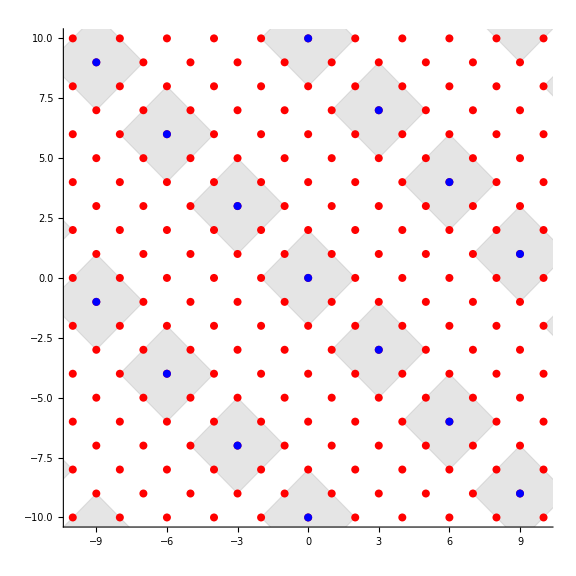

```mathematica
Show[%1042,ImageSize->Large]
```

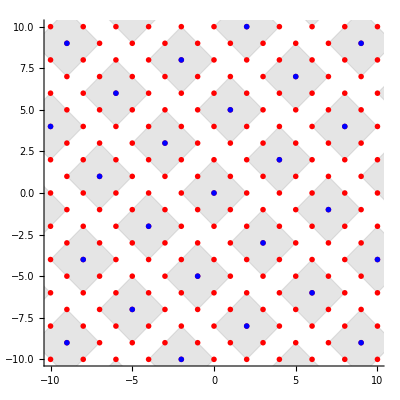

```mathematica
Show[%1003,Background->None]
```

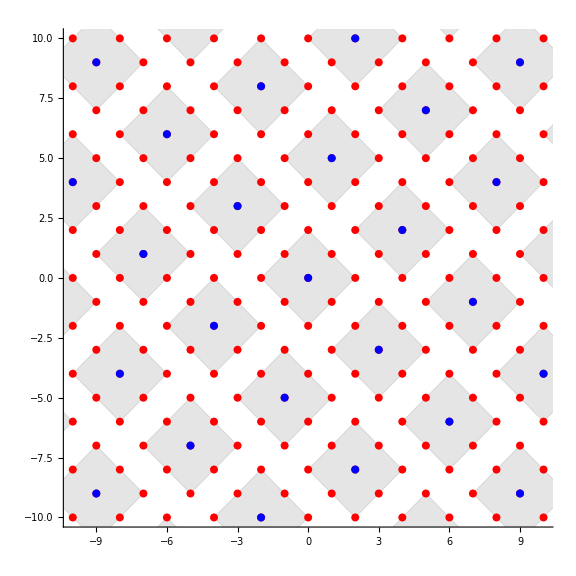

```mathematica
Show[%1004,ImageSize->Large]
```